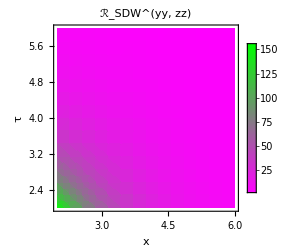

```mathematica
Subscript[a, 0]=10^-3;r=√(x^2+τ^2);v=1;α=0.004;Subscript[y, int]=-0.1;
a=DensityPlot[Cos[α x](Subscript[a, 0]/r)^4*10^16,{x,2,6},{τ,2,6},ColorFunction->(RGBColor[1-#,#,1-#]&),PlotLegends->Automatic,PlotLabel->"ℛ_SDW^(yy, zz)",LabelStyle->Directive[16,Black,FontFamily->"Cambria"],FrameLabel->Automatic,ImageSize->250,PlotRange->Full]
```

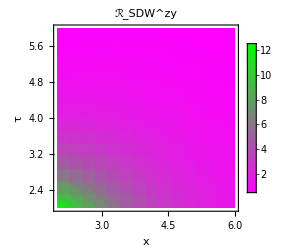

```mathematica
Subscript[a, 0]=10^-3;r=√(x^2+τ^2);v=1;α=0.004;Subscript[y, int]=-0.1;
b=DensityPlot[Sin[α x](Subscript[a, 0]/r)^4*10^17,{x,2.0,6},{τ,2.0,6},ColorFunction->(RGBColor[1-#,#,1-#]&),PlotLegends->Automatic,PlotLabel->"ℛ_SDW^zy",LabelStyle->Directive[16,Black,FontFamily->"Cambria"],FrameLabel->Automatic,ImageSize->250,PlotRange->Full]
```

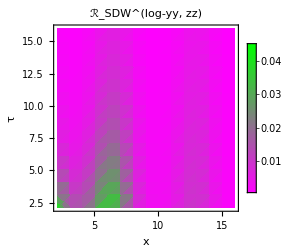

```mathematica
Subscript[a, 0]=10^-3;r=√(x^2+τ^2);v=1;α=0.004;Subscript[y, int]=-0.1;
c=DensityPlot[Cos[α x](Subscript[a, 0]/r)^(4+16 Subscript[y, int])(Subscript[y, int])^-4 Log[Subscript[a, 0]/r]^4 Exp[Cos[Exp[-1/(π Log[r/Subscript[a, 0]])] x]/Cos[α x]-1],{x,2.1,16},{τ,2.1,16},ColorFunction->(RGBColor[1-#,#,1-#]&),PlotLegends->Automatic,PlotLabel->"ℛ_SDW^(log-yy, zz)",LabelStyle->Directive[16,Black,FontFamily->"Cambria"],FrameLabel->Automatic,ImageSize->250,PlotRange->Full]
```

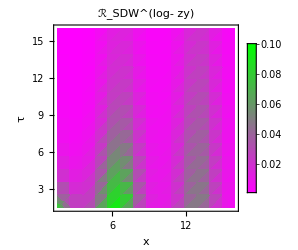

```mathematica
Subscript[a, 0]=10^-3;r=√(x^2+τ^2);v=1;α=0.004;Subscript[y, int]=-0.1;
d=DensityPlot[Sin[α x](Subscript[a, 0]/r)^(4+16 Subscript[y, int])(Subscript[y, int])^-4 Log[Subscript[a, 0]/r]^4 Exp[Cos[Exp[-1/(π Log[r/Subscript[a, 0]])] x]/Cos[α x]-1]*10^2,{x,1.48,16},{τ,1.48,16},ColorFunction->(RGBColor[1-#,#,1-#]&),PlotLegends->Automatic,PlotLabel->"ℛ_SDW^(log- zy)",LabelStyle->Directive[16,Black,FontFamily->"Cambria"],FrameLabel->Automatic,ImageSize->250,PlotRange->Full]
```